# MOT coil calculations

P. Huft

Helmholtz and Anti-Helmholtz coil calculations for designing a coil pair with desired gradient field.  Closed form expressions for finite length solenoids come from Hampton et al. “Closed-form expressions for the magnetic fields
of rectangular and circular finite-length solenoids and current loops”. 

My calculation for nested coils (to approximate a real coil in the lab with multiple layers of wire) neglects the hexagonal packing of the wire that occurs when winding, opting for square packing. This means my results are a lower bound on the field strengths and gradients that can be achieved (in free space).

## setup, functions, and constants

```mathematica
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 15],ImageSize->Medium];

μ0 = 4π*10^-7;
cm = 100;
mm = 1000;

(*field in z from circular coil. SI units*)
BzCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2,u},
n = t/L;
B0 = μ0 i n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/(4π)1/(√(a r))(√m1 ζ1(EllipticK[m1]+((a-r)/(a+r))EllipticPi[u,m1])-√m2 ζ2(EllipticK[m2]+((a-r)/(a+r))EllipticPi[u,m2]))
];
(*field in r from circular coil. SI units*)
BrCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2},
n = t/L;
B0 = μ0 i n;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/π √(a/r)(1/(√m1)(EllipticE[m1]-(1-m1/2)EllipticK[m1])-1/(√m2)(EllipticE[m2]-(1-m2/2)EllipticK[m2]))
];
BxRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
 B0/(8π)Sum[(-1)^(i+j+k)Log[(-(y+ay(-1)^(j+1))+rijk)/(y+ay(-1)^(j+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
ByRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(8π)Sum[(-1)^(i+j+k)Log[(-(x+ax(-1)^(i+1))+rijk)/(x+ax(-1)^(i+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
BzRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,B0,rijk,i,j,k},
B0=μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(4π)Sum[(-1)^(i+j+k+1)(ArcTan[((x+ax(-1)^(i+1))(z+az(-1)^(k+1)))/((y+ay(-1)^(j+1))rijk)]+ArcTan[((y+ay(-1)^(j+1))(z+az(-1)^(k+1)))/((x+ax(-1)^(i+1))rijk)]),{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
```

## quantum network node - parabolic mirror version

## quadrupole coils

Circular coils, each of t turns, length L, and an integer number of layers, arranged to be concentric and separated by distance d with currents of opposite handedness.

```mathematica
(*independent variables*)
L=0.01;(*length, m*)
a= 0.025;(*minimum radius, m*)
dia=0.7/mm; (*wire dia, mm*)
"coil turns (length)"
t=Floor[L/dia+0.5](*turns*)
amps=2;
"coil layers (thickness)"
layers = 7
"coil thickness [mm]"
dia*layers*mm
"coil length"
L*mm
d =0.03; (*center to center coil separation*)
Bz=0;(*the field function*)
Br=0;
Bzlist = {};(*list for storing solenoid field for different number of turns, for debugging*)
Brlist={};

(*just one layered coil for debugging*)
(*For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps](*+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps]*);
Br+=BrCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]Sign[r](*+BrCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps]Sign[r]*);
]*)
(*construct field from a pair of layered coils*)
For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
Br+=BrCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BrCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
]
```

coil turns (length)

14

coil layers (thickness)

7

coil thickness [mm]

4.9

coil length

10.

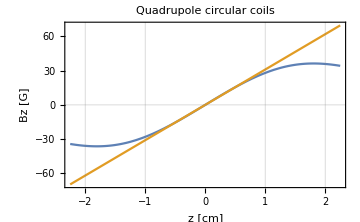

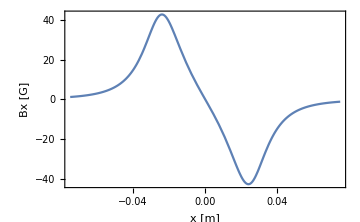

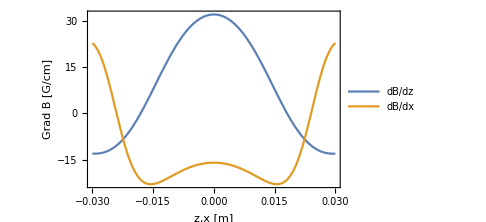

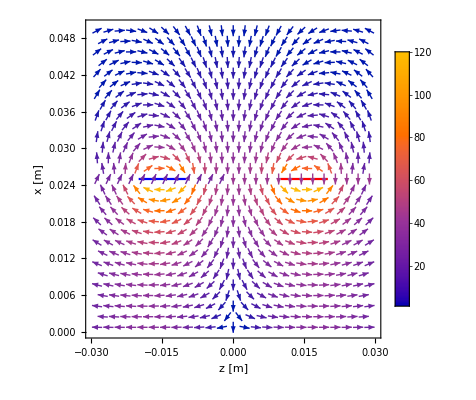

```mathematica
(*Bx can be gotten by plotting sign(x)Br*)
Plot[{10^4 Bz/.{r->10^-8,z->zcm/cm},31 zcm},{zcm,cm*-3d/4,cm*3d/4},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]","Bz [G]"},PlotLabel->"Quadrupole circular coils"]
Plot[10^4 Sign[r]Br/.z->10^-8,{r,-3a,3a},PlotRange->All,FrameLabel->{"x [m]","Bx [G]"}]
Plot[{Evaluate[0.01D[10^4 Bz/.r->10^-8,z]/.z->x],Evaluate[0.01Sign[r]D[10^4 Br/.z->10^-8,r]/.r->x]},{x,-d,d},FrameLabel->{"z,x [m]","Grad B [G/cm]"},PlotLegends->{"dB/dz","dB/dx"}]

(*coil graphics - just a pair of lines representing a coil cross section*)
leftcoil ={ListPlot[{{-(d+L)/2,-a},{-(d-L)/2,-a}},PlotStyle->Blue,Joined->True],ListPlot[{{-(d+L)/2,a},{-(d-L)/2,a}},PlotStyle->Blue,Joined->True]};
rightcoil = {ListPlot[{{(d+L)/2,-a},{(d-L)/2,-a}},PlotStyle->Red,Joined->True],ListPlot[{{(d+L)/2,a},{(d-L)/2,a}},PlotStyle->Red,Joined->True]};

Show[VectorPlot[{10^4 Bz/.r->Abs[x],10^4 Sign[x]Br/.r->x},{z,-d,d},{x,0,2a},PlotLegends->Automatic,FrameLabel->{"z [m]","x [m]"},VectorPoints->Fine],leftcoil,rightcoil,Grid->True]
```

## shim coils

For now, I’ll assume the x and y shim coils each have the same shape. The pairs are arranged in Helmholtz configuration. We are only interested in the peak field along z, defined to be the axis lying perpendicular to the plane of a single loop of the coil. 

The z shims could be the quadrupole coils driven in a helmholtz configuration.

coil turns (length)

14

coil layers (thickness)

5

coil thickness [mm]

3.5

coil length

10.

Peak shim field [G] with 1 amps

2.83817

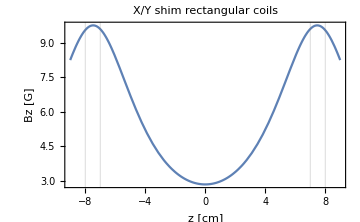

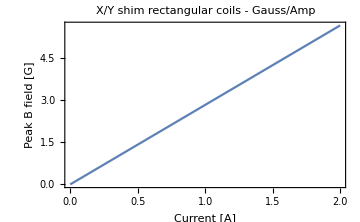

```mathematica
(*X,Y SHIM*)

(*independent variables*)
L=0.01;(*length, m*)
wx= 0.1097;(*x width, m*)
wy= 0.066;(*y width, m*)
dia=0.7/mm; (*wire dia, mm*)
"coil turns (length)"
t=Floor[L/dia+0.5](*turns*)
amps=1;
"coil layers (thickness)"
layers = 5
"coil thickness [mm]"
dia*layers*mm
"coil length"
L*mm
d=0.150;(*coil separation, m*)
Bx=By=Bz=0;
Bxlist =Bylist=Bzlist= {};
(*construct the field from a pair of multi-layer coils*)
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Print["Peak shim field [G] with ", amps," amps"]
10^4 Bz/.{x->0,y->0,z->0}
Plot[10^4 Bz/.{x->0,y->0,z->zcm/cm},{zcm,-cm 1.2d/2,cm 1.2d/2},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]", "Bz [G]"},PlotLabel->"X/Y shim rectangular coils
"]
Clear[amps]
Bz=0;
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Plot[10^4 Bz/.{x->0,y->0,z->0},{amps,0,2},FrameLabel->{"Current [A]", "Peak B field [G]"},PlotLabel->"X/Y shim rectangular coils - Gauss/Amp"]
```

Peak shim field, G

27.0151

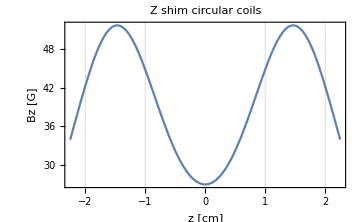

```mathematica
(*Z SHIM*)

(*independent variables*)
amps=2;
L=0.01;(*length, m*)
a= 0.01;(*minimum radius, m*)
t=10;(*turns*)
layers=5;
dia=1/mm;(*wire diameter, mm*)
d =0.03; (*center to center coil separation*)
Bz=0;(*the field function*)
Br=0;
(*construct field from a pair of layered coils*)
For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia,t,amps];
]
"Peak shim field, G"
10^4 Bz/.{r->10^-8,z->0}
Plot[10^4 Bz/.{r->10^-8,z->zcm/cm},{zcm,cm*-3d/4,cm*3d/4},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]","Bz [G]"},PlotLabel->"Z shim circular coils"]
```

## geometry

Geometry calcs for the coil holders that fit around the pancake chamber. See my turquoise Leuchtturm notebook page 221.

```mathematica
R = 151.6/2;
t=2.5;
θt=ArcCos[1-t^2/R^2];
θd=(2π-4θt)/4;
d=R √(2(1-Cos[θd]));
d/(R √2)
d
```

0.976407

104.668

```mathematica
3*25.4*2
```

152.4

## quantum network node - cavity version

## quadrupole coils

Circular coils, each of t turns, length L, and an integer number of layers, arranged to be concentric and separated by distance d with currents of opposite handedness.

```mathematica
(*independent variables*)
L=0.01;(*length, m*)
a= 0.02;(*minimum radius, m*)
dia=0.65/mm; (*wire dia, mm*)
"coil turns (length)"
t=Floor[L/dia+0.5](*turns*)
amps=2;
"coil layers (thickness)"
layers = 12
"total turns"
layers*t
"coil length (mm)"
L*mm
"coil thickness (mm)"
dia*layers*mm
d =20/mm + 2*7.3/mm; (*center to center coil separation = 2 windows 7.3mm thick each and a 20 mm vacuum gap*)
Bz=0;(*the field function*)
Br=0;
Bzlist = {};(*list for storing solenoid field for different number of turns, for debugging*)
Brlist={};

(*just one layered coil for debugging*)
(*For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps](*+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps]*);
Br+=BrCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]Sign[r](*+BrCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps]Sign[r]*);
]*)
(*construct field from a pair of layered coils*)
For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
Br+=BrCircCoil[r,z-d/2,L,a+(i-1)dia*10^-3,t,amps]+BrCircCoil[r,z+d/2,L,a+(i-1)dia*10^-3,t,-amps];
]
```

coil turns (length)

15

coil layers (thickness)

12

total turns

180

coil length (mm)

10.

coil thickness (mm)

7.8

```mathematica
14*0.65
```

9.1

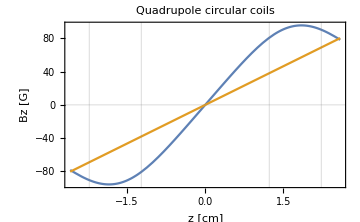

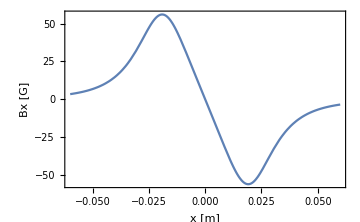

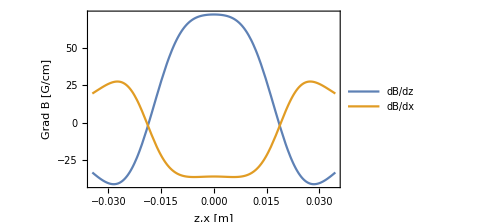

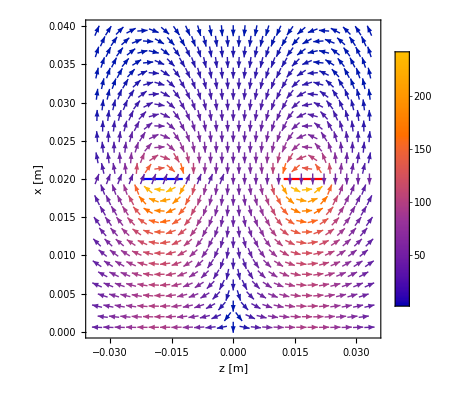

```mathematica
(*Bx can be gotten by plotting sign(x)Br*)
Plot[{10^4 Bz/.{r->10^-8,z->zcm/cm},31 zcm},{zcm,cm*-3d/4,cm*3d/4},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]","Bz [G]"},PlotLabel->"Quadrupole circular coils"]
Plot[10^4 Sign[r]Br/.z->10^-8,{r,-3a,3a},PlotRange->All,FrameLabel->{"x [m]","Bx [G]"}]
Plot[{Evaluate[0.01D[10^4 Bz/.r->10^-8,z]/.z->x],Evaluate[0.01Sign[r]D[10^4 Br/.z->10^-8,r]/.r->x]},{x,-d,d},FrameLabel->{"z,x [m]","Grad B [G/cm]"},PlotLegends->{"dB/dz","dB/dx"}]

(*coil graphics - just a pair of lines representing a coil cross section*)
leftcoil ={ListPlot[{{-(d+L)/2,-a},{-(d-L)/2,-a}},PlotStyle->Blue,Joined->True],ListPlot[{{-(d+L)/2,a},{-(d-L)/2,a}},PlotStyle->Blue,Joined->True]};
rightcoil = {ListPlot[{{(d+L)/2,-a},{(d-L)/2,-a}},PlotStyle->Red,Joined->True],ListPlot[{{(d+L)/2,a},{(d-L)/2,a}},PlotStyle->Red,Joined->True]};

Show[VectorPlot[{10^4 Bz/.r->Abs[x],10^4 Sign[x]Br/.r->x},{z,-d,d},{x,0,2a},PlotLegends->Automatic,FrameLabel->{"z [m]","x [m]"},VectorPoints->Fine],leftcoil,rightcoil,Grid->True]
```

## shim coils

For now, I’ll assume the x and y shim coils each have the same shape. The pairs are arranged in Helmholtz configuration. We are only interested in the peak field along z, defined to be the axis lying perpendicular to the plane of a single loop of the coil. 

The z shims could be the quadrupole coils driven in a helmholtz configuration.

```mathematica
(*X,Y SHIM*)

(*independent variables*)
L=0.01;(*length, m*)
wx= 0.1097;(*x width, m*)
wy= 0.066;(*y width, m*)
dia=0.7/mm; (*wire dia, mm*)
"coil turns (length)"
t=Floor[L/dia+0.5](*turns*)
amps=1;
"coil layers (thickness)"
layers = 5
"coil thickness [mm]"
dia*layers*mm
"coil length"
L*mm
d=0.150;(*coil separation, m*)
Bx=By=Bz=0;
Bxlist =Bylist=Bzlist= {};
(*construct the field from a pair of multi-layer coils*)
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Print["Peak shim field [G] with ", amps," amps"]
10^4 Bz/.{x->0,y->0,z->0}
Plot[10^4 Bz/.{x->0,y->0,z->zcm/cm},{zcm,-cm 1.2d/2,cm 1.2d/2},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]", "Bz [G]"},PlotLabel->"X/Y shim rectangular coils
"]
Clear[amps]
Bz=0;
For[i=1,i<layers+1,i++,
Bz+=BzRectCoil[x,y,z+d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps]+BzRectCoil[x,y,z-d/2,L,wx+2(i-1)dia,wy+2(i-1)dia,t,amps];
]
Plot[10^4 Bz/.{x->0,y->0,z->0},{amps,0,2},FrameLabel->{"Current [A]", "Peak B field [G]"},PlotLabel->"X/Y shim rectangular coils - Gauss/Amp"]
```

coil turns (length)

14

coil layers (thickness)

5

coil thickness [mm]

3.5

coil length

10.

Peak shim field [G] with 1 amps

2.83817

-Graphics-

-Graphics-

```mathematica
(*Z SHIM*)

(*independent variables*)
amps=2;
L=0.01;(*length, m*)
a= 0.01;(*minimum radius, m*)
t=10;(*turns*)
layers=5;
dia=1/mm;(*wire diameter, mm*)
d =0.03; (*center to center coil separation*)
Bz=0;(*the field function*)
Br=0;
(*construct field from a pair of layered coils*)
For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z-d/2,L,a+(i-1)dia,t,amps]+BzCircCoil[r,z+d/2,L,a+(i-1)dia,t,amps];
]
"Peak shim field, G"
10^4 Bz/.{r->10^-8,z->0}
Plot[10^4 Bz/.{r->10^-8,z->zcm/cm},{zcm,cm*-3d/4,cm*3d/4},GridLines->{{{cm(d-L)/2,Thick},{cm(d+L)/2,Thick},{-cm(d-L)/2,Thick},{-cm(d+L)/2,Thick}},{0}},PlotRange->All,FrameLabel->{"z [cm]","Bz [G]"},PlotLabel->"Z shim circular coils"]
```

Peak shim field, G

27.0151

-Graphics-

## geometry

Geometry calcs for the coil holders that fit around the pancake chamber. See my turquoise Leuchtturm notebook page 221.

```mathematica
R = 151.6/2;
t=2.5;
θt=ArcCos[1-t^2/R^2];
θd=(2π-4θt)/4;
d=R √(2(1-Cos[θd]));
d/(R √2)
d
```

0.976407

104.668

```mathematica
3*25.4*2
```

152.4

## misc tests

model a single coil by nested finite solenoids. the radius or width of each nested solenoid is determined by the thickness of wire gauge, even though the expressions here assume infinitesimally thin currents

## circular finite-length solenoids

Single layer coil

```mathematica
Clear[r,z]
(*independent variables*)
L=0.01;(*length, m*)
a= 0.01;(*radius, m*)
t=1;(*turns*)
amps=2;
(*dependent variables*)
n = t/L;
B0 = μ0 amps n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
Br = B0/π √(a/r)(1/(√m1)(EllipticE[m1]-(1-m1/2)EllipticK[m1])-1/(√m2)(EllipticE[m2]-(1-m2/2)EllipticK[m2]));
Bz = B0/(4π)1/(√(a r))(√m1 ζ1(EllipticK[m1]+((a-r)/(a+r))EllipticPi[u,m1])-√m2 ζ2(EllipticK[m2]+((a-r)/(a+r))EllipticPi[u,m2]));
```

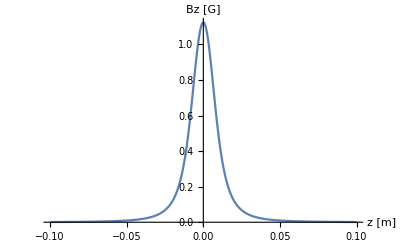

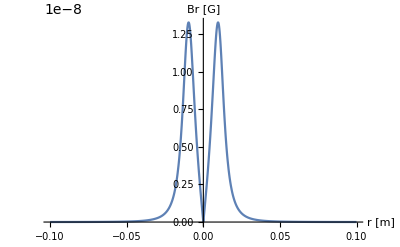

```mathematica
Clear[r,z]
r=10^-10;
Plot[Bz/10^-4,{z,-10L,10L},PlotRange->All,AxesLabel->{"z [m]","Bz [G]"}]
Clear[r,z]
z=10^-10;
Plot[Br/10^-4,{r,-10a,10a},AxesLabel->{"r [m]","Br [G]"},PlotRange->All]
```

Coil modules

```mathematica
BzCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2},
n = t/L;
B0 = μ0 i n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/(4π)1/(√(a r))(√m1 ζ1(EllipticK[m1]+((a-r)/(a+r))EllipticPi[u,m1])-√m2 ζ2(EllipticK[m2]+((a-r)/(a+r))EllipticPi[u,m2]))
];
BrCircCoil[r_,z_,length_,radius_,turns_,amps_]:=Module[{L=length,a=radius,t=turns,i=amps,n,B0,ζ1,ζ2,m1,m2,u},
n = t/L;
B0 = μ0 i n;
u = (4a r)/(a+r)^2;
ζ1 = z+L/2;
ζ2 = z-L/2;
m1 = (4 a r)/((a+r)^2+ζ1^2);
m2 = (4 a r)/((a+r)^2+ζ2^2);
B0/π √(a/r)(1/(√m1)(EllipticE[m1]-(1-m1/2)EllipticK[m1])-1/(√m2)(EllipticE[m2]-(1-m2/2)EllipticK[m2]))
];
```

-Graphics-

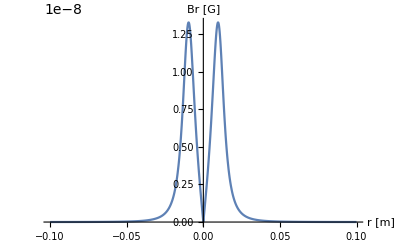

```mathematica
(*independent variables*)
L=0.01;(*length, m*)
a= 0.01;(*minimum radius, m*)
t=1;(*turns*)
amps=2;

Clear[r,z]
Plot[BzCircCoil[10^-10,z,L,a,t,amps]/10^-4,{z,-10L,10L},PlotRange->All,AxesLabel->{"z [m]","Bz [G]"}]
Plot[BrCircCoil[r,10^-10,L,a,t,amps]/10^-4,{r,-10 a,10 a},PlotRange->All,AxesLabel->{"r [m]","Br [G]"}]
```

Multi-layer (nested) solenoids

```mathematica
Clear[r,z]
(*independent variables*)
L=0.01;(*length, m*)
a= 0.01;(*minimum radius, m*)
t=1;(*turns*)
amps=2;
layers=4;
dia=1;(*wire diameter, mm*)
Bz=0;(*the field function*)
Br=0;
Bzlist = {};(*list for storing solenoid field for different number of turns, for debugging*)
Brlist={};
(*construct field from layered coil*)
For[i=1,i<layers+1,i++,
Bz+=BzCircCoil[r,z,L,a+(i-1)dia*10^-3,t,amps];
Br+=BrCircCoil[r,z,L,a+(i-1)dia*10^-3,t,amps];
AppendTo[Bzlist,Bz];
AppendTo[Brlist,Br];
]
```

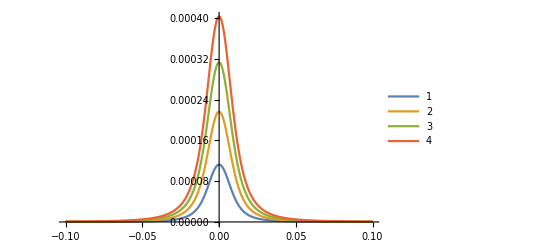

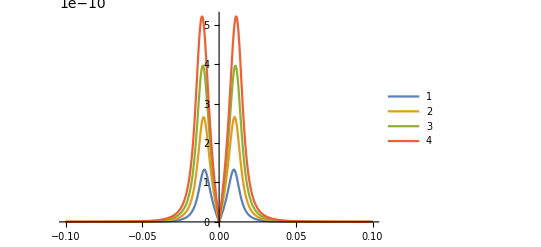

```mathematica
Clear[r,z];
Plot[Evaluate[Bzlist/.r->10^-8],{z,-10L,10L},PlotLegends->Range[layers],PlotRange->All]
Plot[Evaluate[Brlist/.z->10^-8],{r,-10a,10a},PlotLegends->Range[layers],PlotRange->All]
```

## rectangular finite-length solenoids

Reproduce the example from the paper

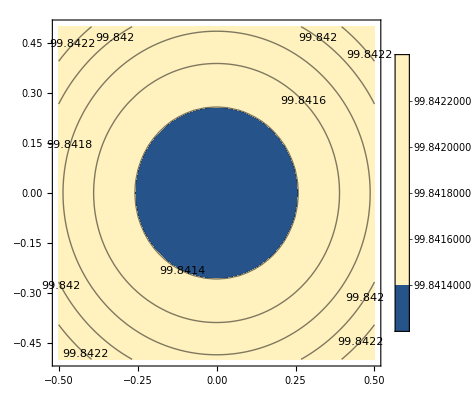

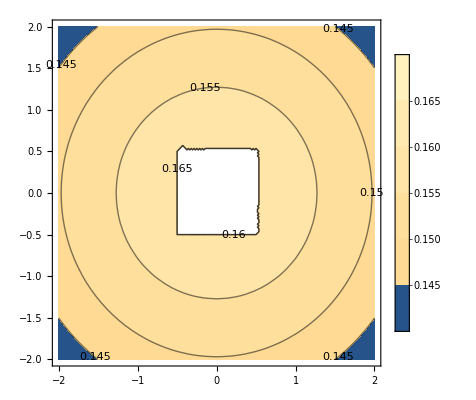

```mathematica
Clear[x,y,z,i,j,k]
(*independent variables*)
L=20;(*length, m*)
wx= 1;(*x width, m*)
wy= 1;(*y width, m*)
t=1;(*turns*)
amps=2;
(*dependent variables*)
az = L/2;
ax = wx/2;
ay = wy/2;
n = t/L;
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
Bx = B0/(8π)Sum[(-1)^(i+j+k)Log[(-(y+ay(-1)^(j+1))+rijk)/(y+ay(-1)^(j+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}];
By = B0/(8π)Sum[(-1)^(i+j+k)Log[(-(x+ax(-1)^(i+1))+rijk)/(x+ax(-1)^(i+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}];
Bz = B0/(4π)Sum[(-1)^(i+j+k+1)(ArcTan[((x+ax(-1)^(i+1))(z+az(-1)^(k+1)))/((y+ay(-1)^(j+1))rijk)]+ArcTan[((y+ay(-1)^(j+1))(z+az(-1)^(k+1)))/((x+ax(-1)^(i+1))rijk)]),{i,{0,1}},{j,{0,1}},{k,{0,1}}];
Clear[x,y,z]
ContourPlot[(100√(Bx^2+By^2+Bz^2)/B0)/.z->0,{x,-ax,ax},{y,-ay,ay},PlotLegends->Automatic,ContourLabels->True]
ContourPlot[(100√(Bx^2+By^2+Bz^2)/B0)/.z->0,{x,-4ax,4ax},{y,-4ay,4ay},PlotLegends->Automatic,ContourLabels->True]
```

Coil modules

```mathematica
BzRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,i,j,k},
B0=μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(4π)Sum[(-1)^(i+j+k+1)(ArcTan[((x+ax(-1)^(i+1))(z+az(-1)^(k+1)))/((y+ay(-1)^(j+1))rijk)]+ArcTan[((y+ay(-1)^(j+1))(z+az(-1)^(k+1)))/((x+ax(-1)^(i+1))rijk)]),{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
BxRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
 B0/(8π)Sum[(-1)^(i+j+k)Log[(-(y+ay(-1)^(j+1))+rijk)/(y+ay(-1)^(j+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
ByRectCoil[x_,y_,z_,length_,wx_,wy_,turns_,amps_]:=Module[{L=length,ax=wx/2,ay=wy/2,az=L/2,n=turns/length,i,j,k},
B0 = μ0 amps n;
rijk = √((x+ax(-1)^(i+1))^2+(y+ay(-1)^(j+1))^2+(z+az(-1)^(k+1))^2);
B0/(8π)Sum[(-1)^(i+j+k)Log[(-(x+ax(-1)^(i+1))+rijk)/(x+ax(-1)^(i+1)+rijk)],{i,{0,1}},{j,{0,1}},{k,{0,1}}]
];
```

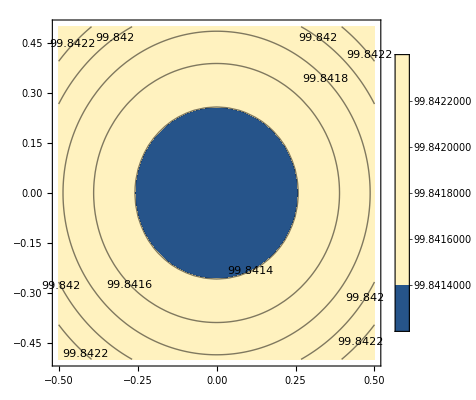

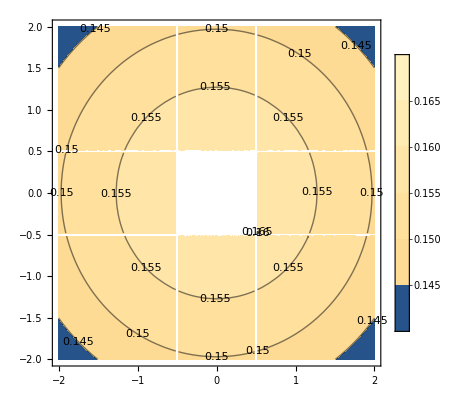

```mathematica
(*independent variables*)
L=20;(*length, m*)
wx= 1;(*x width, m*)
wy= 1;(*y width, m*)
t=1;(*turns*)
amps=2;
B0=μ0 amps t/L;
ContourPlot[(100√(BxRectCoil[x,y,0,L,wx,wy,t,amps]^2+ByRectCoil[x,y,0,L,wx,wy,t,amps]^2+BzRectCoil[x,y,0,L,wx,wy,t,amps]^2)/B0),{x,-ax,ax},{y,-ay,ay},PlotLegends->Automatic,ContourLabels->True]
ContourPlot[(100√(BxRectCoil[x,y,0,L,wx,wy,t,amps]^2+ByRectCoil[x,y,0,L,wx,wy,t,amps]^2+BzRectCoil[x,y,0,L,wx,wy,t,amps]^2)/B0),{x,-4ax,4ax},{y,-4ay,4ay},PlotLegends->Automatic,ContourLabels->True]
```

Multi-layer coils

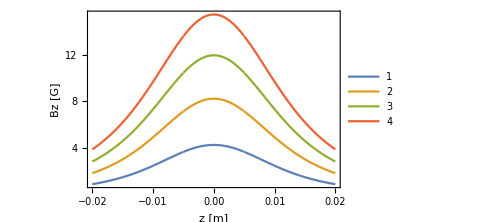

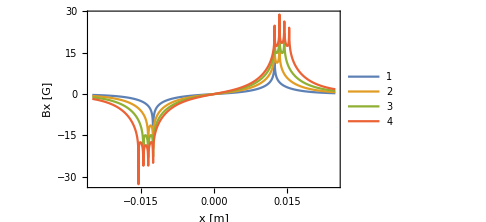

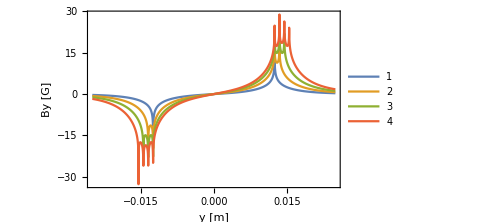

```mathematica
(*independent variables*)
L=0.01;(*length, m*)
wx= 0.025;(*x width, m*)
wy= 0.025;(*y width, m*)
t=10;(*turns*)
amps=1;
layers = 4;
dia=1; (*wire dia, mm*)
Bx=By=Bz=0;
Bxlist =Bylist=Bzlist= {};
For[i=1,i<layers+1,i++,
Bx+=BxRectCoil[x,y,z,L,wx+2(i-1)dia*10^-3,wy+2(i-1)dia*10^-3,t,amps];
AppendTo[Bxlist,Bx];
By+=ByRectCoil[x,y,z,L,wx+2(i-1)dia*10^-3,wy+2(i-1)dia*10^-3,t,amps];
AppendTo[Bylist,By];
Bz+=BzRectCoil[x,y,z,L,wx+2(i-1)dia*10^-3,wy+2(i-1)dia*10^-3,t,amps];
AppendTo[Bzlist,Bz];
]
Plot[Evaluate[10^4 Bzlist/.{x->0,y->0}],{z,-2L,2L},PlotLegends->Range[layers],PlotRange->All,FrameLabel->{"z [m]", "Bz [G]"}]
Plot[Evaluate[10^4 Bxlist/.{z->L/2,y->0}],{x,-wx,wx},PlotLegends->Range[layers],PlotRange->All,FrameLabel->{"x [m]", "Bx [G]"}]
Plot[Evaluate[10^4 Bylist/.{z->L/2,x->0}],{y,-wy,wy},PlotLegends->Range[layers],PlotRange->All,FrameLabel->{"y [m]", "By [G]"}]
```

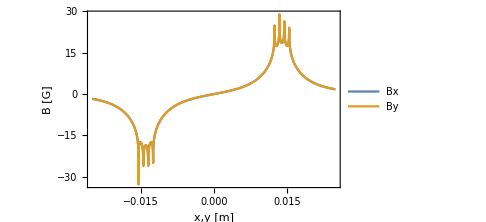

```mathematica
Plot[{10^4 Bx/.{z->L/2,y->0,x->u},10^4 By/.{z->L/2,y->u,x->0}},{u,-wx,wx},PlotLegends->{"Bx","By"},PlotRange->All,FrameLabel->{"x,y [m]", "B [G]"}]
```

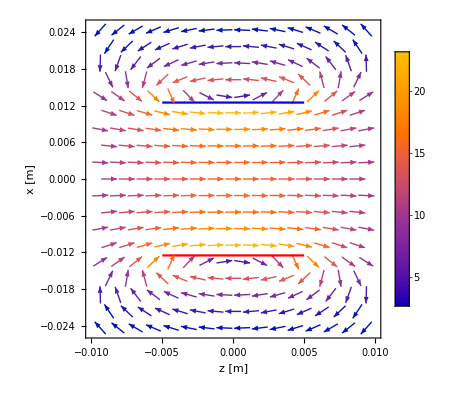

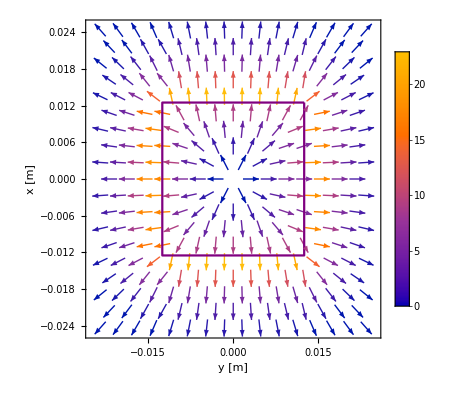

```mathematica
coilyx =ListPlot[{{wy/2,wx/2},{wy/2,-wx/2},{-wy/2,-wx/2},{-wy/2,wx/2},{wy/2,wx/2}},PlotStyle->Purple,Joined->True];
d=0;
coilzx = {ListPlot[{{(d+L)/2,-wx/2},{(d-L)/2,-wx/2}},PlotStyle->Red,Joined->True],ListPlot[{{(d+L)/2,wx/2},{(d-L)/2,wx/2}},PlotStyle->Blue,Joined->True]};
Show[VectorPlot[{10^4 Bz/.y->0,10^4 Bx/.y->0},{z,-L,L},{x,-wx,wx},PlotLegends->Automatic,FrameLabel->{"z [m]","x [m]"}],coilzx]
Show[VectorPlot[{10^4 By/.z->L/2,10^4 Bx/.z->L/2},{y,-wy,wy},{x,-wx,wx},PlotLegends->Automatic,FrameLabel->{"y [m]","x [m]"}],coilyx]
```

```mathematica
Table[{21+0.55*mins,mins},{mins,Range[0,180,10]}]
```

{{21.,0},{26.5,10},{32.,20},{37.5,30},{43.,40},{48.5,50},{54.,60},{59.5,70},{65.,80},{70.5,90},{76.,100},{81.5,110},{87.,120},{92.5,130},{98.,140},{103.5,150},{109.,160},{114.5,170},{120.,180}}